# Analysis of Data

## Jonathan Pincince

## C++ Validation

This section’s for validation of the C++ code I wrote to compute the derivative of a function. I’ll be using the same cosine function as I did for the first assignment, as well a polynomial function.

```mathematica
SetDirectory[NotebookDirectory[]];
FileNames[]
```

{Analysis.nb,cosad.txt,cosd.txt,flat_bounce1.txt,flat_bounce2.txt,flat_bounce3.txt,flat_bounce4.txt,flat_bounce5.txt,Modeling.nb,pd.txt}

## Cosine Function

```mathematica
f[x_]:=Cos[0.01 x^2+1]/x
cosExactPoints=Import["cosd.txt","Table"];
cosApproxPoints=Import["cosad.txt","Table"];
```

### ‘Exact’ Derivative Method

```mathematica
MMADerivs={};
CDerivs={};
AbsDerivDiffs={};
RelDerivDiffs={};
CosInputs=Table[cosExactPoints[[9*k]][[1]],{k,1,10}];
CDerivOutputs=Table[cosExactPoints[[9*k]][[2]],{k,1,10}];

For[k=1,k<=Dimensions[CosInputs][[1]],k++,
MMAD=f'[CosInputs[[k]]];
CD=CDerivOutputs[[k]];
AbsErr=CD-MMAD;
RelErr=(100*AbsErr)/MMAD;
MMADerivs=Append[MMADerivs,{CosInputs[[k]],MMAD}];
CDerivs=Append[CDerivs,{CosInputs[[k]],CD}];
AbsDerivDiffs=Append[AbsDerivDiffs,{AbsErr}];
RelDerivDiffs=Append[RelDerivDiffs,{RelErr}];
]
Print["An x value followed by the derivative of the function at that point, as computed by Mathematica."];
MMADerivs
Print["An x value followed by derivative at that point, this time as computed by the C++ program using the 'exact' implementation, where dfunc() has been overwritten by the child class."];
CDerivs
Print["The absolute difference between Mathematica's derivative and the C++ computed value."];
AbsDerivDiffs
Print["The relative error of the C++ calculation as percentages. These are all less than a percent of a percent, so I'd say the C++ program is doing a reasonably good job."];
RelDerivDiffs
```

An x value followed by the derivative of the function at that point, as computed by Mathematica.

{{0.9,-0.67552},{1.8,-0.17543},{2.7,-0.0830832},{3.6,-0.051034},{4.5,-0.0364379},{5.4,-0.0286763},{6.3,-0.0240577},{7.2,-0.0209828},{8.09999,-0.0186287},{9,-0.0165055}}

An x value followed by derivative at that point, this time as computed by the C++ program using the 'exact' implementation, where dfunc() has been overwritten by the child class.

{{0.9,-0.67552},{1.8,-0.17543},{2.7,-0.0830832},{3.6,-0.0510341},{4.5,-0.036438},{5.4,-0.0286763},{6.3,-0.0240577},{7.2,-0.0209828},{8.09999,-0.0186287},{9,-0.0165055}}

The absolute difference between Mathematica's derivative and the C++ computed value.

{{-2.20543×10^-7},{-1.46373×10^-7},{1.45095×10^-8},{-7.81397×10^-8},{-7.09199×10^-8},{-2.89437×10^-8},{-2.2969×10^-8},{2.17329×10^-8},{1.4673×10^-8},{-1.08673×10^-8}}

The relative error of the C++ calculation as percentages. These are all less than a percent of a percent, so I'd say the C++ program is doing a reasonably good job.

{{0.0000326479},{0.000083437},{-0.0000174638},{0.000153113},{0.000194632},{0.000100933},{0.0000954748},{-0.000103575},{-0.0000787655},{0.0000658406}}

### Approximate Derivative Method

```mathematica
MMADerivsApprox={};
CDerivsApprox={};
AbsDerivDiffsApprox={};
RelDerivDiffsApprox={};
RelErrorDiffs={};
CosInputs=Table[cosApproxPoints[[9*k]][[1]],{k,1,10}];
CDerivOutputs=Table[cosApproxPoints[[9*k]][[2]],{k,1,10}];

For[k=1,k<=Dimensions[CosInputs][[1]],k++,
MMAD=f'[CosInputs[[k]]];
CD=CDerivOutputs[[k]];
AbsErr=CD-MMAD;
RelErr=(100*AbsErr)/MMAD;
MMADerivsApprox=Append[MMADerivsApprox,{CosInputs[[k]],MMAD}];
CDerivsApprox=Append[CDerivsApprox,{CosInputs[[k]],CD}];
AbsDerivDiffsApprox=Append[AbsDerivDiffsApprox,{AbsErr}];
RelDerivDiffsApprox=Append[RelDerivDiffsApprox,{RelErr}];
RelErrorDiffs=Append[RelErrorDiffs,{RelDerivDiffs[[k]]-RelErr}];
]
Print["An x value followed by the derivative of the function at that point, as computed by Mathematica."];
MMADerivsApprox
Print["An x value followed by derivative at that point, this time as computed by the C++ program using the 'approximate' implementation, where dfunc() uses Function1D's approximation."];
CDerivsApprox
Print["The absolute difference between Mathematica's derivative and the C++ computed value."];
AbsDerivDiffsApprox
Print["The relative error of the C++ calculation as percentages. Again, these relative errors are tiny values."];
RelDerivDiffsApprox
Print["The difference between the relative errors of the 'exact' dfunc method vs. Function1D's approximation. Surprisingly, most of these differences are positive, meaning that the relative error of the 'exact' method is actually larger than the approximate method for most tested inputs, but this isn't always the case."];
RelErrorDiffs
```

An x value followed by the derivative of the function at that point, as computed by Mathematica.

{{0.9,-0.67552},{1.8,-0.17543},{2.7,-0.0830832},{3.6,-0.051034},{4.5,-0.0364379},{5.4,-0.0286763},{6.3,-0.0240577},{7.2,-0.0209828},{8.09999,-0.0186287},{9,-0.0165055}}

An x value followed by derivative at that point, this time as computed by the C++ program using the 'approximate' implementation, where dfunc() uses Function1D's approximation.

{{0.9,-0.675519},{1.8,-0.175428},{2.7,-0.083085},{3.6,-0.0510313},{4.5,-0.0364383},{5.4,-0.0286754},{6.3,-0.024058},{7.2,-0.0209821},{8.09999,-0.0186278},{9,-0.0165054}}

The absolute difference between Mathematica's derivative and the C++ computed value.

{{7.79457×10^-7},{1.85363×10^-6},{-1.78549×10^-6},{2.72186×10^-6},{-3.7092×10^-7},{8.71056×10^-7},{-3.22969×10^-7},{7.21733×10^-7},{9.14673×10^-7},{8.91327×10^-8}}

The relative error of the C++ calculation as percentages. Again, these relative errors are tiny values.

{{-0.000115386},{-0.00105662},{0.00214904},{-0.00533342},{0.00101795},{-0.00303755},{0.00134248},{-0.00343964},{-0.00491002},{-0.000540018}}

The difference between the relative errors of the 'exact' dfunc method vs. Function1D's approximation. Surprisingly, most of these differences are positive, meaning that the relative error of the 'exact' method is actually larger than the approximate method for most tested inputs, but this isn't always the case.

{{{0.000148034}},{{0.00114006}},{{-0.0021665}},{{0.00548654}},{{-0.000823318}},{{0.00313848}},{{-0.001247}},{{0.00333606}},{{0.00483125}},{{0.000605859}}}

## Polynomial Function

## The Bouncing Ball

```mathematica
FileNames[]
```

{Analysis.nb,cosad.txt,cosd.txt,flat_bounce1.txt,flat_bounce2.txt,flat_bounce3.txt,flat_bounce4.txt,flat_bounce5.txt,Modeling.nb,pd.txt}

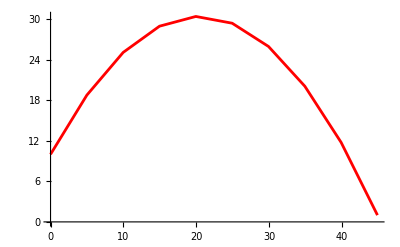

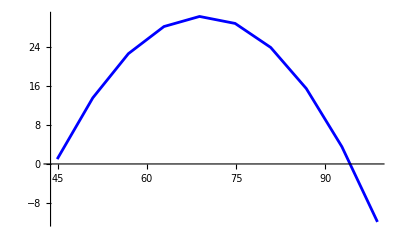

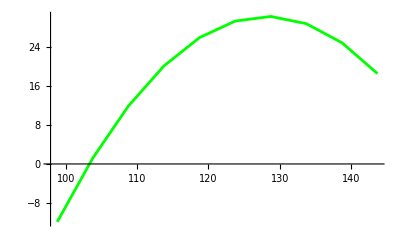

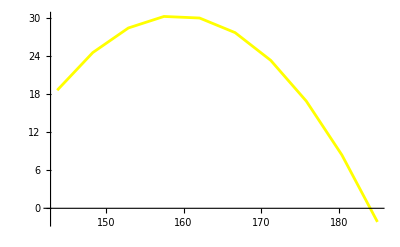

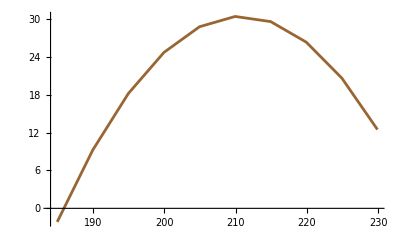

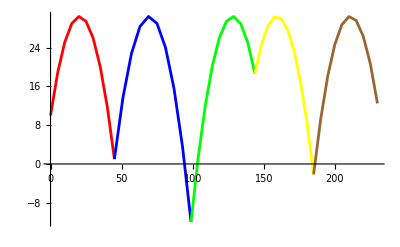

```mathematica
trajectory1:=Import["flat_bounce1.txt","Table"]
trajectory2:=Import["flat_bounce2.txt","Table"]
trajectory3:=Import["flat_bounce3.txt","Table"]
trajectory4:=Import["flat_bounce4.txt","Table"]
trajectory5:=Import["flat_bounce5.txt","Table"]
plotT1=ListLinePlot[trajectory1,PlotStyle->Red]
plotT2=ListLinePlot[trajectory2,PlotStyle->Blue]
plotT3=ListLinePlot[trajectory3,PlotStyle->Green]
plotT4=ListLinePlot[trajectory4,PlotStyle->Yellow]
plotT5=ListLinePlot[trajectory5,PlotStyle->Brown]
Show[{plotT1,plotT2,plotT3,plotT4,plotT5},PlotRange->All]
```

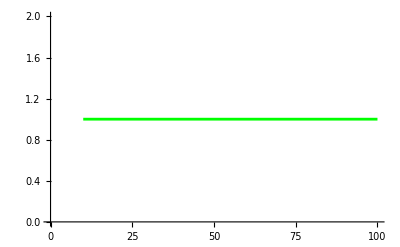

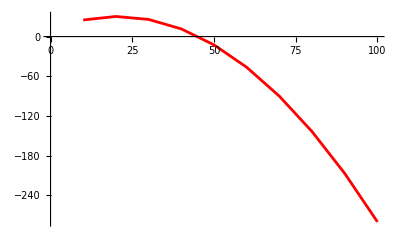

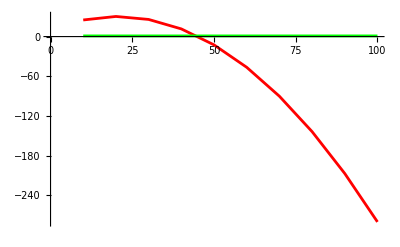

```mathematica
flat[x_]:=x^0;
surfacePts={};
xPos=0;
yPos=10;
posPts={};
For[t=1,t<=10,t++,
surfacePts=Append[surfacePts,{t*10,flat[t*10]}];
posPts=Append[posPts,{xPos+(10*t),yPos+(20*t)-(4.9*t*t)}];
]
plotSurface=ListLinePlot[surfacePts,PlotStyle->Green]
plotPts=ListLinePlot[posPts,PlotStyle->Red]
Show[{plotPts,plotSurface}]
```